```mathematica
L=128;
```

```mathematica
m=Sqrt[.25];
```

```mathematica
Λ=2
```

2

## 2D

```mathematica
prop[{q_,r_}]:=1/(Λ(k2[q]+k2[r])^2+k2[q]+k2[r]+m^2)
```

```mathematica
Clear[k2]
```

```mathematica
k2[q_]:=k2[q]=2-2Cos[2Pi q/L]
```

### Tree level

```mathematica
(sum[1]=ParallelSum[prop[{q,r}]//N,{q,0,L-1},{r,0,L-1}]/(L^2) )//Timing
```

{0.432027,0.137383}

```mathematica
sum[1]
```

0.137383

### One loop

```mathematica
sum[2]=ParallelSum[prop[{q,r}]^2,{q,0,L-1},{r,0,L-1}]/(L^2)
```

0.186469

```mathematica
corrphi2[1,g_,n_]=-1/2 g sum[2] sum[1](2n +n^2)/3
```

-0.0042696 g (2 n+n^2)

### Two loops

#### Saturn

```mathematica
saturn[n_]=1/6 sum[1]^3(6n + 3 n^2)/9
```

0.0000480179 (6 n+3 n^2)

### Cactus

```mathematica
cactus[n_]=1/4(n^3 + 4 n^2 +4 n) sum[2]^2sum[1]/9
```

0.000132691 (4 n+4 n^2+n^3)

### Tadpole 2

```mathematica
sum[3]=ParallelSum[prop[{q,r}]^3,{q,0,L-1},{r,0,L-1}]/(L^2)
```

0.459487

```mathematica
tadpole[2,n_]=1/4 (4 n+4 n^2+n^3)/9sum[3]sum[1]^2
```

0.0002409 (4 n+4 n^2+n^3)

```mathematica
corrphi2[2,g_,n_]=g^2 (saturn[n]+cactus[n]+tadpole[2,n])
```

g^2 (0.0000480179 (6 n+3 n^2)+0.00037359 (4 n+4 n^2+n^3))

## Plots

```mathematica
corrphi2[1,0.1,3]
```

-0.00640439

```mathematica
corrphi2[2,0.1,3]
```

0.000301801

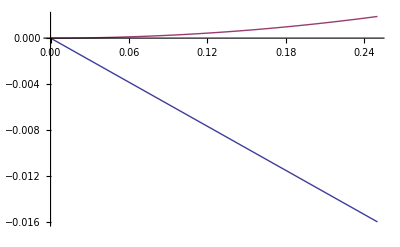

```mathematica
Plot[{corrphi2[1,g,3],corrphi2[2,g,3]},{g,0,.25}]
```

```mathematica
corrphi2[g_,n_]=corrphi2[1,g,n]+corrphi2[2,g,n]
```

-0.0042696 g (2 n+n^2)+g^2 (0.0000480179 (6 n+3 n^2)+0.00037359 (4 n+4 n^2+n^3))

```mathematica
corrphi2[0.1,3]
```

-0.00610259

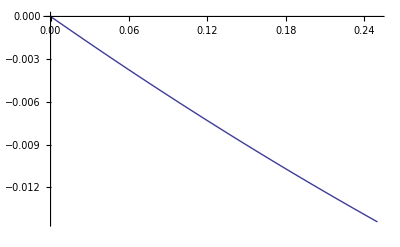

```mathematica
Plot[{corrphi2[g,3]},{g,0,.25}]
```

```mathematica
corrphi2[0.25,3]
```

-0.0141247

## 3D

```mathematica
ParallelSum[1.0/(Λ(k2[q]+k2[r]+k2[t])^2+k2[q]+k2[r]+k2[t]+m^2),{q,0,L-1},{r,0,L-1},{t,0,L-1}]/(L^3)
```

$Aborted